# ASC Presentation

```mathematica
ClearAll["Global`*"]
meshLevel=1;
title="voronoi";
```

```mathematica
SetDirectory["/home/alexander/Documents/LaTeX/ASC/img"];
Needs["NDSolve`FEM`"]
Omega=Rectangle[];
path="/home/alexander/Documents/Amanzi/build-amanzi/build-amanzi-xmof/src/operators/"<>title<>"_"<>ToString@meshLevel;
```

```mathematica
Get["https://raw.githubusercontent.com/dih5/TgBot/master/TgBot/TgBot.m"];
Needs["TgBot`"]
tgChatID=Import["/home/alexander/Documents/Wolfram Mathematica/tg.txt","List"][[1]];
tgToken=Import["/home/alexander/Documents/Wolfram Mathematica/tg.txt","List"][[2]];
BotAPICall["getUpdates",{},{"Token"->tgToken}];
```

## Import Geometry

```mathematica
geometryFile=Import[path<>"_geometry.dat"];
numbOfNodes=geometryFile[[1,1]];
numbOfCells=geometryFile[[1,2]];
nodes=geometryFile[[2;;numbOfNodes+1]];
cells=geometryFile[[numbOfNodes+2;;numbOfCells+numbOfNodes+1]];
matIDs=geometryFile[[numbOfCells+numbOfNodes+2;;2numbOfCells+numbOfNodes+1]]//Flatten;
centroids=geometryFile[[2numbOfCells+numbOfNodes+2;;3numbOfCells+numbOfNodes+1]];
numbOfIntNodes=geometryFile[[3numbOfCells+numbOfNodes+2,1]];
numbOfIntFaces=geometryFile[[3numbOfCells+numbOfNodes+2,2]];
intNodes=geometryFile[[3numbOfCells+numbOfNodes+3;;3numbOfCells+numbOfNodes+numbOfIntNodes+2]];
intFaces=geometryFile[[-numbOfIntFaces;;]];
```

```mathematica
region=MeshRegion[nodes,Polygon/@cells];
Show[region,Graphics[Point/@centroids]]
```

## Import Soln

```mathematica
soln=Import[path<>"_solution.dat"]//Flatten;
```

```mathematica
polygons=Polygon/@Table[nodes[[cells[[i]]]],{i,numbOfCells}];
```

```mathematica
normSoln=(soln-Min@soln)/(Max@soln-Min@soln);
colorFunc="TemperatureMap";
solPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->{Thin,Gray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@normSoln],PlotLegends->BarLegend@{colorFunc,{Min@soln,Max@soln}}]
matPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->{LightGray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@((matIDs-1)/(Max@matIDs-1))]]
```

## Convergence

```mathematica
computeRefMeanVals[u_,polygons_]:=Module[{n=Length@polygons,res},
Monitor[res=Table[NIntegrate[u[x,y],{x,y}∈polygons[[i]]]/Area[polygons[[i]]],{i,n}],ProgressIndicator[i,{1,n}]];
BotAPICall["sendMessage",{"chat_id"->tgChatID,"text"->"computeRefMeanVals[]: finished for "<>ToString@n<>" elements"},{"Token"->tgToken}];
res
]
L2Norm[u_,v_,polygons_]:=Module[{n=Length@polygons,res},
Monitor[res=Sqrt@Total@Table[(u[[i]]-v[[i]])^2 Area@polygons[[i]],{i,n}],ProgressIndicator[i,{1,n}]];
BotAPICall["sendMessage",{"chat_id"->tgChatID,"text"->"L2Norm[]: finished for "<>ToString@n<>" elements"},{"Token"->tgToken}];
res
]
```

### voronoi .1 / .6 k = .01

```mathematica
h={0.236316,0.112098,0.0637145,0.031974,0.015624};
err0={0.0213188,0.0100664,0.00623111,0.00307565,0.00110878};
err1={0.00111499,0.000148555,2.75572*10^(-5),2.63772*10^(-5),5.24184*10^(-6)};
```

```mathematica
h=h[[;;-2]];
err0=err0[[;;-2]];
err1=err1[[;;-2]];
```

```mathematica
h1=Transpose@{h,.05(#)^(1)&/@h};
h2=Transpose@{h,.005(#)^(2)&/@h};
```

```mathematica
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0)",20],Style["ASC(1)",20]}]
```

```mathematica
Export["convplot.png",Show[convPlot,ImageSize->500]]
```

```mathematica
ScientificForm[h,2]
```

```mathematica
plot=RegionPlot[Evaluate@polygons,BoundaryStyle->{Thin,Gray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@normSoln],PlotLegends->BarLegend@{colorFunc,{Min@soln,Max@soln}}]
```

```mathematica
Export["skew_acs1_4.png",Show[plot,ImageSize->500]]
```

```mathematica
Export["skew_asc1.png",Show[-Graphics-,ImageSize->500]]
```

### skewed .1 / .9 square / k2 = .1

```mathematica
u1[x_,y_]:=x+y
{U1,U2,U3}=LinearSolve[{{.1,0,1},{.9,1,1},{1,0,1}},{1,1,91}];
u2[x_,y_]:=U1 x+U2 y+U3
V[x_,y_]:={x,y}-{.1,0}
U={.9,1}-{.1,0};
u[x_,y_]:=Piecewise[{{u1[x,y], U[[1]]V[x,y][[2]]-U[[2]]V[x,y][[1]]>0}, {u2[x,y], True}}]
```

```mathematica
uMax=First@NMaximize[u[x,y],{x,y}∈Omega];
uMin=First@NMinimize[u[x,y],{x,y}∈Omega];
bndryPlotEps=.005;
bndryPlot=RegionPlot[Polygon[{{.1-bndryPlotEps,0},{.1+bndryPlotEps,0},{.9+bndryPlotEps,1},{.9-bndryPlotEps,1}}],PlotStyle->{ColorData["TemperatureMap",(u2[.1,0]-uMin)/(uMax-uMin)]},BoundaryStyle->None,PlotPoints->100];
```

```mathematica
refPlot=DensityPlot[u[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,PlotPoints->100];
```

```mathematica
Show[refPlot,bndryPlot]
```

```mathematica
Export["skew_ref.png",Show[refPlot,bndryPlot,ImageSize->500]]
```

```mathematica
Sqrt[.25^2+.25^2]
```

```mathematica
h={0.353553,(*0.176777,*)0.0883883,(*0.0441942,*)0.0220971,(*0.0110485,*)0.00552427};
(*longest face (base + minimesh)*)
(*h={(*0.640312,*)0.320156,0.160078,0.0800391,0.0400195};*)
(* rel error *)
(*err0={0.0270509,0.0278391,0.0135894,0.00593663,0.00285437};
err1={0.00410982,0.000942437,0.000390866,7.22483*10^-05,2.35823*10^-05};*)
err0={0.727194,(*0.361733,*)0.15884,(*0.076474,*)0.0365133,(*0.0180318,*)0.00890009};
err0inf={4.83587,(*3.70255,*)1.20751,(*0.578169,*)0.337077,(*0.231141,*)0.0786085};
err1={0.0246177,(*0.0104044,*)0.00193307,(*0.000631815,*)0.000162533,(*5.7894*10^(-5),*)1.34772*10^(-5)};
err1inf={0.156458,(*0.388502,*)0.0632055,(*0.0169284,*)0.0098103,(*0.0242869,*)0.00395083};
h1=Transpose@{h,.3(#)^(1)&/@h};
h2=Transpose@{h,.06(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
order0=Table[(Log[err0[[i]]]-Log[err0[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
order1=Table[(Log[err1[[i]]]-Log[err1[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
```

```mathematica
Export["skew_conv_square.png",Show[convPlot,ImageSize->800]]
```

```mathematica
ScientificForm[err1inf,2]
```

### skewed .1 / .9 voronoi + mesh ref

```mathematica
h={0.278042,0.132956,0.06296,0.0324147,0.0180366};
(* rel error *)
(*err0={0.0120092,0.00352876,0.00242205,0.0021474,0.00108145};
err1={0.000439326,0.00012818,5.77925*10^-05,1.51601*10^-05,4.24611*10^-06};*)
err0={0.317071,0.0942179,0.0648524,0.0575432,0.0289853};
err0inf={2.44054,1.02242,1.00093,0.673394,0.420805};
err1={0.0115993,0.0034224,0.00154744,0.00040624,0.000113805};
err1inf={0.15094,0.0912247,0.0898461,0.0141871,0.0127115};
h1=Transpose@{h,.5(#)^(1)&/@h};
h2=Transpose@{h,.06(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
Export["skew_conv_voronoi.png",Show[convPlot,ImageSize->500]]
```

```mathematica
ScientificForm[err1inf,2]
```

### skewed .1 / .9 triangular + mesh ref

```mathematica
h={(*0.353553,*)0.179215,0.102423,0.0566351,0.0275459};
(* rel error *)
(*err0={0.0890488,0.0674669,0.0261182,0.00939423,0.00551769};
err1={0.00094089,0.000373116,7.84425*10^-05,3.15574*10^-05,6.35106*10^-06};*)
err0={(*2.35217,*)1.79845,0.699136,0.25172,0.147885};
err0inf={(*7.13779,*)6.18554,2.99604,1.35381,0.839575};
err1={(*0.024853,*)0.00994605,0.00209976,0.000845584,0.000170221};
err1inf={(*0.167101,*)0.408609,0.0738543,0.0212875,0.0409371};
h1=Transpose@{h,.5(#)^(1)&/@h};
h2=Transpose@{h,.06(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
Export["skew_conv_triangular.png",Show[convPlot,ImageSize->500]]
```

```mathematica
ScientificForm[err1inf,2]
```

### skewed .11 / .91 triangular_int + mesh ref (Robustness test)

```mathematica
h={(*0.390312,*)0.207931,0.0996334,0.0499461,0.0279358};
err0={(*1.54077,*)1.6869,0.743995,0.381735,0.118416};
err0inf={(*9.22721,*)5.12514,3.50931,1.45502,0.838609};
err1={(*0.00302407,*)0.00265833,0.00279064,0.00132479,0.000189185};
err1inf={(*0.26005,*)0.258147,0.251332,0.135121,0.0122482};
h1=Transpose@{h,1.5(#)^(1)&/@h};
h2=Transpose@{h,.006(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
order0=Table[(Log[err0[[i]]]-Log[err0[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
order1=Table[(Log[err1[[i]]]-Log[err1[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
```

```mathematica
Export["skew_conv_rob_01.png",Show[convPlot,ImageSize->500]]
```

```mathematica
ScientificForm[err1inf,2]
```

### skewed .101 / .901 triangular_int + mesh ref (Robustness test)

```mathematica
h={(*0.390312,*)0.215728,0.107431,0.0500961,0.0279325};
err0={(*0.965421,*)0.897321,0.354558,0.296889,0.176059};
err0inf={(*12.4112,*)8.06737,4.75314,2.26337,0.891194};
err1={(*4.76906*10^-05,*)4.03152*10^-05,5.56595*10^-05,5.65594*10^-05,5.57393*10^-05};
err1inf={(*0.042711,*)0.0426747,0.0425323,0.040304,0.0306182};
h1=Transpose@{h,1.5(#)^(1)&/@h};
h2=Transpose@{h,.006(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
order0=Table[(Log[err0[[i]]]-Log[err0[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
order1=Table[(Log[err1[[i]]]-Log[err1[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
```

```mathematica
Export["skew_conv_rob_001.png",Show[convPlot,ImageSize->500]]
```

```mathematica
ScientificForm[err1inf,2]
```

### circle voronoi k2 = .001

```mathematica
k1=1;
k2=.001;
u2[x_,y_]:=(x-1/2)^2+(y-1/2)^2-1/25
u1[x_,y_]:=k2/k1 u2[x,y]
```

```mathematica
u[x_,y_]:=Piecewise[{{u1[x,y], (x-1/2)^2+(y-1/2)^2>1/25}, {u2[x,y], True}}]
```

```mathematica
refPlot=DensityPlot[u[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,PlotPoints->100];
```

```mathematica
uMax=First@NMaximize[u[x,y],{x,y}∈Omega]
uMin=First@NMinimize[u[x,y],{x,y}∈Omega]
```

```mathematica
bndryPlot=RegionPlot[(x-1/2)^2+(y-1/2)^2≤1/25,{x,0,1},{y,0,1},BoundaryStyle->{ColorData["TemperatureMap",(u2[.7,.5]-uMin)/(uMax-uMin)],Thickness@.008},PlotStyle->Transparent,PlotPoints->100];
```

```mathematica
Show[refPlot,bndryPlot]
```

```mathematica
Export["circle_ref.png",Show[refPlot,bndryPlot,ImageSize->500]]
```

```mathematica
Show[refPlot,bndryPlot,meshPlot]
```

```mathematica
Export["circle_ref_mesh.png",Show[refPlot,bndryPlot,meshPlot,ImageSize->500]]
```

```mathematica
refPlotSlice=Plot[u[x,.5],{x,0,1},PlotStyle->{Thick},ColorFunction->"TemperatureMap",AxesLabel->{"x",None}]
```

```mathematica
Export["circle_ref_slice.png",Show[refPlotSlice,ImageSize->500]]
```

```mathematica
Timing[solnRef=computeRefMeanVals[u,polygons];]
```

```mathematica
L2Norm[solnRef,soln,polygons]
```

```mathematica
h={0.2521,0.114978,0.0658193,0.0336591,0.00870148};
h={0.29984,0.154633,0.0814022,0.0419896,0.0211456,0.0104733};
(* mathematica nintegrate -- linear conv 
err0={0.0043388224872396965,0.002266328434280937,0.0013112479594015482,0.0006875990796442551};
err1={0.004349881737827885,0.002279714857973929,0.0013052402422879027,0.0006767898525012529};
*)
(* cpp 
err0={0.000685588,0.000317427,0.00024907,0.000149669};
err1={0.000502185,0.000264995,0.000109593,3.94019*10^-05};
*)
(* mathematica -- mean values *)
err0={0.0023791996260904224,0.000652996374690894,0.00025923997492990723,0.0001394197624040473,0.00003703973316449299,0.0000272247};
err0inf={0.00633433,0.00704921,0.00319981,0.00226639,0.00113936,0.000857562};
err1={0.0023993085295655483,0.0006980397747103584,0.00022690580355237607,0.00006848270055360247,0.00002012526370139414,5.367952367229611*^-6};
err1inf={0.00214415,0.0133219,0.00067808,0.000320176,0.000111836,3.32967*10^-05};
h1=Transpose@{h,.01(#)^(1)&/@h};
h2=Transpose@{h,.015(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,asc0inf,asc1inf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","○","□"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Opacity@.4,Opacity@.4}]
```

```mathematica
order0=Table[(Log[err0[[i]]]-Log[err0[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
order1=Table[(Log[err1[[i]]]-Log[err1[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}]
```

```mathematica
Export["circle_conv_voronoi.png",Show[convPlot,ImageSize->800]]
```

```mathematica
ScientificForm[err1inf,2]
```

### ring triangles k2 = .001, k1 = k3 = 1

```mathematica
k1=1;
k2=.001;
k3=1;
u3[x_,y_]:=(x-1/2)^2+(y-1/2)^2-9/400
u2[x_,y_]:=k3/k2 u3[x,y]
u1[x_,y_]:=k3/k1((x-1/2)^2+(y-1/2)^2-1/25)+u2[.7,.5]
```

```mathematica
u[x_,y_]:=Piecewise[{{u1[x,y], (x-1/2)^2+(y-1/2)^2>1/25}, {u2[x,y], (x-1/2)^2+(y-1/2)^2>9/400}, {u3[x,y], True}}]
```

```mathematica
uMax=First@NMaximize[u[x,y],{x,y}∈Omega]
uMin=First@NMinimize[u[x,y],{x,y}∈Omega]
```

```mathematica
bndryPlot1=RegionPlot[(x-1/2)^2+(y-1/2)^2≤1/25,{x,0,1},{y,0,1},BoundaryStyle->{ColorData["TemperatureMap",(u2[.7,.5]-uMin)/(uMax-uMin)],Thickness@.008},PlotStyle->Transparent,PlotPoints->100];
bndryPlot2=RegionPlot[(x-1/2)^2+(y-1/2)^2≤9/400,{x,0,1},{y,0,1},BoundaryStyle->{ColorData["TemperatureMap",(u[.5+.15,.5]-uMin)/(uMax-uMin)],Thickness@.008},PlotStyle->Transparent,PlotPoints->100];
```

```mathematica
refPlot=DensityPlot[u[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,PlotPoints->200]
Plot[u[x,.5],{x,0,1},PlotStyle->{Red,Thick},AxesLabel->{"x",None}]
```

```mathematica
Export["ring_ref_mesh.png",Show[refPlot,bndryPlot1,bndryPlot2,meshPlot,ImageSize->500]]
```

```mathematica
Timing[solnRef=computeRefMeanVals[u,polygons];]
```

```mathematica
Export["solnRef_ring_"<>ToString@title<>"_"<>ToString@meshLevel<>".dat",solnRef]
```

```mathematica
solnRef=Import["solnRef_ring_"<>ToString@title<>"_"<>ToString@meshLevel<>".dat","List"];
```

```mathematica
L2Norm[solnRef,soln,polygons]
```

```mathematica
h={0.273579,0.195705,0.109308,0.0803261,0.0591141,(*0.0526696,*)0.039699};
h={0.300666,0.25,0.125,0.0833333,0.0666667,0.0434783};
(* mathematica -- mean values *)
errHA={4.9437339271815794,4.958258301243894,4.933014292571722,4.728989612886983,4.354044243034639,0.9662909542114478};
errHAinf={17.2581,17.2485,17.1757,16.9948,15.78,5.73628};
errHH={2.2972406833114927,1.7086187025212578,0.7288755167325357,0.48386741954330253,0.3359811626509772,0.16385842467184542};
errHHinf={14.6811,15.9614,12.3543,11.6408,9.36478,8.19344};
err0={4.511668617244358,4.503245342825646,4.045967631732087,4.386924458154012,0.7117786522700738,(*0.6960034682588425,*)0.44656439734253817};
err0inf={17.1612,17.1112,16.5846,16.7481,4.93945,(*5.4678,*)5.0251};
err1={0.453553681443837,0.2619493109307899,0.09205973697907037,0.04840027597488361,0.027595385903684964,(*0.023120451945307523,*)0.010449165443050317};
err1inf={3.52479,2.70101,0.617443,0.828906,0.226026,(*0.428356,*)0.0631747};
h1=Transpose@{h,3.(#)^(1)&/@h};
h2=Transpose@{h,2.8(#)^(2)&/@h};
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
asc0inf=Transpose@{h,err0inf};
asc1inf=Transpose@{h,err1inf};
HA=Transpose@{h,errHA};
HAinf=Transpose@{h,errHAinf};
HH=Transpose@{h,errHH};
HHinf=Transpose@{h,errHHinf};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1,HA,HH,asc0inf,asc1inf,HAinf,HHinf},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■","▲","▼","○","□","△","▽"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0) L2",20],Style["ASC(1) L2",20],Style["A-HOM L2",20],Style["H-HOM L2",20],Style["ASC(0) ∞",20],Style["ASC(1) ∞",20],Style["A-HOM ∞",20],Style["H-HOM ∞",20]},PlotStyle->{Automatic,Automatic,Thick,Thick,Thick,Thick,Opacity@.4,Opacity@.4,Opacity@.4,Opacity@.4}]
```

```mathematica
order0=Table[(Log[err0[[i]]]-Log[err0[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
order1=Table[(Log[err1[[i]]]-Log[err1[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
orderA=Table[(Log[errHA[[i]]]-Log[errHA[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
orderH=Table[(Log[errHH[[i]]]-Log[errHH[[i+1]]])/(Log[h[[i]]]-Log[h[[i+1]]]),{i,Length@h-1}];
```

```mathematica
Export["ring_conv_triangular.png",Show[convPlot,ImageSize->800]]
```

```mathematica
ScientificForm[order1,2]
```

## Temp Output

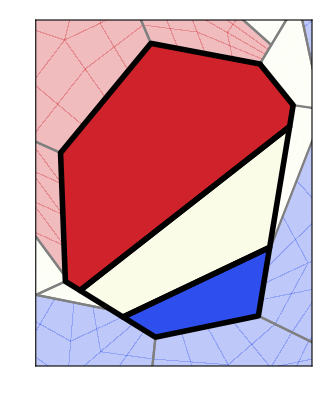
```mathematica
Export["ring_mini_voronoi_cell.png",Show[-Graphics-,ImageSize->500]]
```

```mathematica
meshPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->Gray,PlotStyle->Evaluate[{ColorData[colorFunc,#],Opacity@.3}&/@((matIDs-1)/(Max@matIDs-1))],
FrameTicks->None,PlotRange->{{.43,.69},{.25,.57}},AspectRatio->Automatic,FrameStyle->{{Thick,Gray},{Thick,Gray},{Thick,Gray},{Thick,Gray}}]
```

```mathematica
matPlot=Show[meshPlot,RegionPlot[Evaluate@polygons[[43;;45]],BoundaryStyle->{Black,Thickness@.01},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@{0,1/2,1}],Frame->False]]
```

```mathematica
Export["skew_geometry_square.png",Show[matPlot,ImageSize->500]]
```

```mathematica
matPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->{LightGray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@((matIDs-1)/(Max@matIDs-1))],PlotRange->{{.2,.4},{.4,.6}}]
```

```mathematica
Export["skew_rob_4.png",Show[matPlot,ImageSize->500]]
```

```mathematica
max=0.00045999999999999996;
min=-0.04;
normSoln=(soln-min)/(max-min);
```

```mathematica
solPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->{Thick,LightGray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@normSoln],PlotLegends->BarLegend@{colorFunc,{min,max}},PlotRange->{{.2,.4},{.4,.6}}]
```

```mathematica
Export["circle_voronoi_2_asc0.png",Show[solPlot,ImageSize->500]]
```

```mathematica
meshPlot=RegionPlot[Evaluate@polygons,BoundaryStyle->{Black,Thin},PlotStyle->Transparent]
```

### E^+ and E^-

```mathematica
eps=.05;
w=.15;
EPlusNodes={{0,0},{1,0},{1,1},{0,1},
{.2,.0},{.6,0},{1,.5-eps},{1,.5+eps},{.5,1}};
EPlusPolygons=Polygon/@{EPlusNodes[[{1,5,9,4}]],EPlusNodes[[{5,6,7,8,9}]],EPlusNodes[[{6,2,7}]],EPlusNodes[[{8,3,9}]]};
EMinNodes={{1+w,0},{2+w,0},{2+w,1},{1+w,1},{1+w,.5},{2+w,.6}};
EMinPolygons=Polygon/@{EMinNodes[[{1,2,6,5}]],EMinNodes[[{5,6,3,4}]]};
EPolygons=Join[EPlusPolygons,EMinPolygons];
EK={1,2,3,4,3,4};
```

```mathematica
ELeftPCNodes={{-1-w,0},{0-w,0},{0-w,1},{-1-w,1}};
ELeftPCPolygons=Polygon/@{ELeftPCNodes[[{1,2,3,4}]]};
ELeftPCK={1,2,3,4,1};
```

```mathematica
ELeftMMCNodes={{-1-w,0},{0-w,0},{0-w,1},{-1-w,1},{-1-w,.5},{-0-w,.9},{-0-w,.1}};
ELeftMMCPolygons=Polygon/@{ELeftMMCNodes[[{1,2,7,5}]],ELeftMMCNodes[[{5,7,6,5}]],ELeftMMCNodes[[{3,4,5,6}]]};
ELeftMMCK={1,2,3,4,2,1,2};
```

```mathematica
matPlot=RegionPlot[Evaluate@EPolygons,BoundaryStyle->{Black},PlotStyle->Evaluate[ColorData["TemperatureMap",#]&/@((EK-1)/(Max@EK-1))],AspectRatio->Automatic,Frame->False]
matPlotPlus=RegionPlot[Evaluate@EPlusPolygons,BoundaryStyle->{Black},PlotStyle->Evaluate[ColorData["TemperatureMap",#]&/@((EK-1)/(Max@EK-1))],AspectRatio->Automatic,Frame->False]
matPlotLeftPC=RegionPlot[Evaluate[Join[EPlusPolygons,ELeftPCPolygons]],BoundaryStyle->{Black},PlotStyle->Evaluate[ColorData["TemperatureMap",#]&/@((ELeftPCK-1)/(Max@ELeftPCK-1))],
AspectRatio->Automatic,Frame->False,PlotRange->{{-2w,1.01},Automatic}]
matPlotLeftMMC=RegionPlot[Evaluate[Join[EPlusPolygons,ELeftMMCPolygons]],BoundaryStyle->{Black},PlotStyle->Evaluate[ColorData["TemperatureMap",#]&/@((ELeftMMCK-1)/(Max@ELeftMMCK-1))],AspectRatio->Automatic,Frame->False,PlotRange->{{-2w,1.01},Automatic}]
```

```mathematica
Export["e_plus_e_minus.png",Show[matPlot,ImageSize->1000]]
```

```mathematica
Export["e_plus.png",Show[matPlotPlus,ImageSize->500]]
```

```mathematica
Export["e_plus_1.png",Show[matPlotLeftPC,ImageSize->500]]
Export["e_plus_2.png",Show[matPlotLeftMMC,ImageSize->500]]
```

### First Slide

```mathematica
plot=RegionPlot[Evaluate@polygons,BoundaryStyle->{LightGray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@((matIDs-1)/(Max@matIDs-1))]]
```

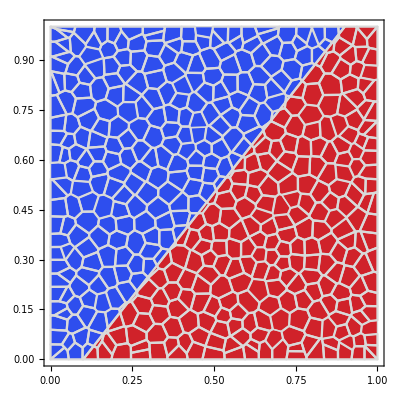
```mathematica
Export["skew_geometry.png",Show[-Graphics-,ImageSize->500]]
```

### Sec Slide

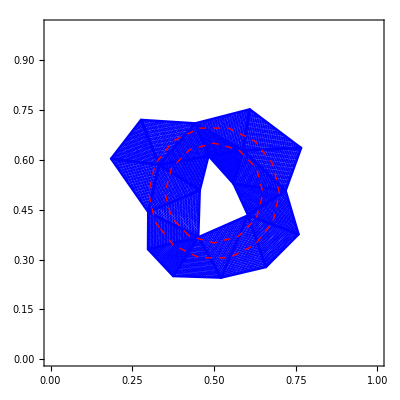
```mathematica
ringMMCsPlot=-Graphics-;
```

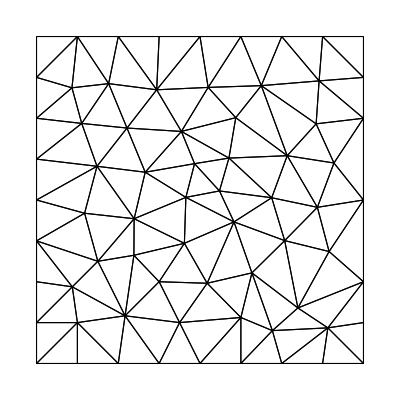
```mathematica
baseMeshPlot=-Graphics-;
ringMiniPlot=-Graphics-;
```

```mathematica
Export["ring_mmcs.png",Show[ringMMCsPlot,ImageSize->500]]
Export["ring_base.png",Show[baseMeshPlot,ImageSize->500]]
Export["ring_mini.png",Show[ringMiniPlot,ImageSize->500]]
```

```mathematica
k1=1;
k2=.001;
k3=1;
u3[x_,y_]:=(x-1/2)^2+(y-1/2)^2-9/400
u2[x_,y_]:=k3/k2 u3[x,y]
u1[x_,y_]:=k3/k1((x-1/2)^2+(y-1/2)^2-1/25)+u2[.7,.5]
```

```mathematica
u[x_,y_]:=Piecewise[{{u1[x,y], (x-1/2)^2+(y-1/2)^2>1/25}, {u2[x,y], (x-1/2)^2+(y-1/2)^2>9/400}, {u3[x,y], True}}]
```

```mathematica
refPlot=DensityPlot[u[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,PlotPoints->500]
```

```mathematica
uMax=First@NMaximize[u[x,y],{x,y}∈Omega];
uMin=First@NMinimize[u[x,y],{x,y}∈Omega];
```

```mathematica
bndryPlotInner=RegionPlot[(x-1/2)^2+(y-1/2)^2≤9/400,{x,0,1},{y,0,1},BoundaryStyle->{ColorData["TemperatureMap",(u2[.65,.5]-uMin)/(uMax-uMin)],Thickness@.008},PlotStyle->Transparent,PlotPoints->100];
bndryPlotOuter=RegionPlot[(x-1/2)^2+(y-1/2)^2≤1/25,{x,0,1},{y,0,1},BoundaryStyle->{ColorData["TemperatureMap",(u2[.7,.5]-uMin)/(uMax-uMin)],Thickness@.008},PlotStyle->Transparent,PlotPoints->100];
```

```mathematica
Show[refPlot,bndryPlotInner,bndryPlotOuter]
```

```mathematica
Export["ring_ref.png",Show[refPlot,bndryPlotInner,bndryPlotOuter,ImageSize->500]]
```

```mathematica
refPlotSlice=Plot[u[x,.5],{x,0,1},PlotStyle->{Thick},ColorFunction->"TemperatureMap",AxesLabel->{"x",None}]
```

```mathematica
Export["ring_ref_slice.png",Show[refPlotSlice,ImageSize->500]]
```

```mathematica
plot=RegionPlot[Evaluate@polygons,BoundaryStyle->{Thin,Gray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@normSoln],PlotLegends->BarLegend@{colorFunc,{Min@soln,Max@soln}}]
```

```mathematica
Export["ring_asc1.png",Show[plot,ImageSize->500]]
```

### Spectrum

```mathematica
plot=RegionPlot[Evaluate@polygons,BoundaryStyle->{LightGray},PlotStyle->Evaluate[ColorData[colorFunc,#]&/@((matIDs-1)/(Max@matIDs-1))]]
```

```mathematica
Export["skew001.png",Show[plot,ImageSize->500]]
```

```mathematica
mtx=Import["/home/alexander/Documents/Amanzi/build-amanzi/build-amanzi-xmof/src/operators/mtx.txt","MTX"];
eig=Eigenvalues@mtx;
```

```mathematica
cond=Max@eig/Min@eig
cond=Max@eig/Min@eig[[;;-4]]
```

```mathematica
w={.1,.01,.001,.0001,.00001};
```

```mathematica
w+.25
```

```mathematica
cond0=Transpose@{w,{41.05047488437758,45.16535625906743,48.342051671357524,49.022979252820015,49.09889500082324}};
cond1=Transpose@{w,{1729.5412198083193,2816.944114506362,16390.58113334854,152324.98574317776,1.5116940844111133*^6}};
eCond1=Transpose@{w,{41.022877350671614,45.12057193278319,48.34003313380988,49.022954141414786,49.09889474389424}};
w1=Transpose@{w,(#/5)^(-1)&/@w};
```

```mathematica
logPlot=ListLogLogPlot[{cond1,w1},Joined->{True,True},Ticks->{{.00001,.0001,.001,.01},Automatic},AxesLabel->{"w",None}, PlotMarkers->{"●",""},PlotLegends->{Style["κ_(ASC (1))(w)",20],Style["O(w^-1)",20]}]
```

```mathematica
Export["logplot.png",Show[logPlot,ImageSize->500]]
```

### w = .01 + mesh ref

```mathematica
h={0.25,0.125,0.0625,0.03125};
err0={0.0328902,0.0219584,0.0115383,0.00417283};
err1={6.74391*10^-5,8.627*10^-5,7.27333*10^-5,2.93052*10^-5};
```

```mathematica
h1=Transpose@{h,.05(#)^(1)&/@h};
h2=Transpose@{h,.005(#)^(2)&/@h};
```

```mathematica
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{".",".","●","■"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0)",20],Style["ASC(1)",20]}]
```

### w = 0.015625 + mesh ref

```mathematica
0.03125/2
```

```mathematica
.25+0.03125/2
```

```mathematica
h={0.25,0.125,0.0625,0.03125};
err0={0.0328902,0.0219584,0.0115383,0.00417283};
err1={0.000157625,0.000175742,0.000106394,1.50953*10^-11};
```

```mathematica
h1=Transpose@{h,.05(#)^(1)&/@h};
h2=Transpose@{h,.005(#)^(2)&/@h};
```

```mathematica
asc0=Transpose@{h,err0};
asc1=Transpose@{h,err1};
```

```mathematica
convPlot=ListLogLogPlot[{h1,h2,asc0,asc1},Joined->True,Ticks->{h,Automatic},AxesLabel->{"h",None}, PlotMarkers->{"","","●","■"},PlotLegends->{Style["O(h)",20],Style["O(h^2)",20],Style["ASC(0)",20],Style["ASC(1)",20]}]
```